## Forced damped oscillations and resonance

```mathematica
Remove["Global`*"]
```

general solution of the ODE

```mathematica
sol1 = DSolve[{x''[t]+2*β*x'[t]+ω0^2*x[t]==A*Cos[ω*t],x[0]==0, x'[0]==0},x[t],t]
```

{{x[t]→-(A (ⅇ^(t (-β-√(β^2-ω0^2))) β ω^2-ⅇ^(t (-β+√(β^2-ω0^2))) β ω^2+ⅇ^(t (-β-√(β^2-ω0^2))) β ω0^2-ⅇ^(t (-β+√(β^2-ω0^2))) β ω0^2+ⅇ^(t (-β-√(β^2-ω0^2))) ω^2 √(β^2-ω0^2)+ⅇ^(t (-β+√(β^2-ω0^2))) ω^2 √(β^2-ω0^2)-ⅇ^(t (-β-√(β^2-ω0^2))) ω0^2 √(β^2-ω0^2)-ⅇ^(t (-β+√(β^2-ω0^2))) ω0^2 √(β^2-ω0^2)-2 ω^2 √(β^2-ω0^2) Cos[t ω]+2 ω0^2 √(β^2-ω0^2) Cos[t ω]+4 β ω √(β^2-ω0^2) Sin[t ω]))/(2 √(β^2-ω0^2) (2 β^2+ω^2-ω0^2+2 β √(β^2-ω0^2)) (-2 β^2-ω^2+ω0^2+2 β √(β^2-ω0^2)))}}

plot of x[t] for beta =0.1, omega =omega0 =2Pi and A =1

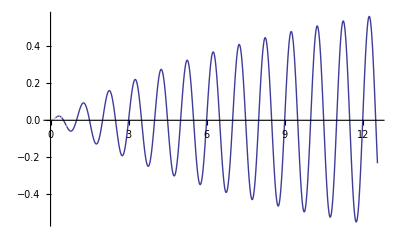

```mathematica
Plot[x[t]/.sol1/.{A->1, ω0->2*Pi,β->0.1, ω->2*Pi},{t,0,4*Pi}]
```

NOTE : the manipulate function seems to dynamically update itself depending on what is being plotted and since I have reused x[t] later on in this notebook, the plots might not look like what is expected. I request you to run the first question only to arrive at the expected solutions while using manipulate.

using manipulate to vary the damping parameter

```mathematica
Manipulate[Plot[x[t]/.sol1/.{A->1,ω0->2*Pi,ω->2*Pi,β->β0},{t,0,4*Pi}],{β0,.1,10}]
```

using manipulate to vary the driving force time period

```mathematica
Manipulate[Plot[x[t]/.sol1/.{A->1,ω0->2*Pi,ω->ω1,β->0.1},{t,0,4*Pi}],{ω1,Pi, 4*Pi}]
```

## Humped potential well

```mathematica
Remove["Global`*"]
```

first case : |x0| << b/2a

```mathematica
x0 =0.01;a=1;b=1;m=1;
```

```mathematica
sol1 = NDSolve[{m*x''[t]==a*x[t]^2-b*x[t],x[0]==x0, x'[0]==0},x,{t,0,20}]
```

{{x→InterpolatingFunction[{{0.,20.}},<>]}}

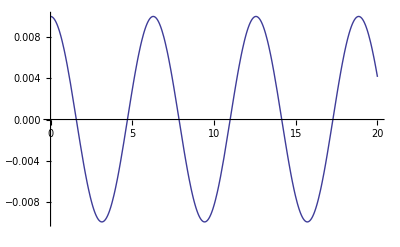

```mathematica
Plot[x[t]/.sol1, {t,0,20}]
```

second case : x0 > -b/2a

NDSolve::ndsz: At t == 9.13172, step size is effectively zero; singularity or stiff system suspected.

{{x→InterpolatingFunction[{{0.,9.13172}},<>]}}

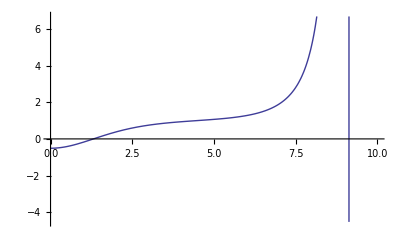

```mathematica
x0 =-0.51;a=1;b=1;m=1;
sol1 = NDSolve[{m*x''[t]==a*x[t]^2-b*x[t],x[0]==x0, x'[0]==0},x,{t,0,10}]
Plot[x[t]/.sol1, {t,0,10}]
```

third case : x0 < b/2a

{{x→InterpolatingFunction[{{0.,20.}},<>]}}

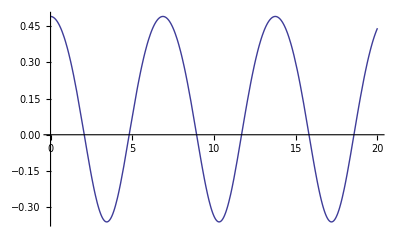

```mathematica
x0 =0.49;a=1;b=1;m=1;
sol1 = NDSolve[{m*x''[t]==a*x[t]^2-b*x[t],x[0]==x0, x'[0]==0},x,{t,0,20}]
Plot[x[t]/.sol1, {t,0,20}]
```

special case : x0 = b/2a

{{x→InterpolatingFunction[{{0.,20.}},<>]}}

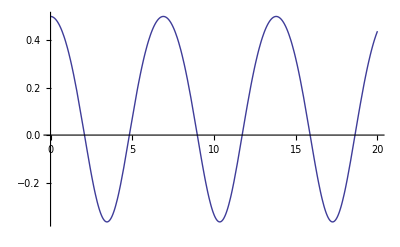

```mathematica
x0 =0.5;a=1;b=1;m=1;
sol1 = NDSolve[{m*x''[t]==a*x[t]^2-b*x[t],x[0]==x0, x'[0]==0},x,{t,0,20}]
Plot[x[t]/.sol1, {t,0,20}]
```

behavior of the force F(x) and the potential energy U(x) over x

```mathematica
Integrate[{-(a*x^2-b*x)},x]
```

{x^2/2-x^3/3}

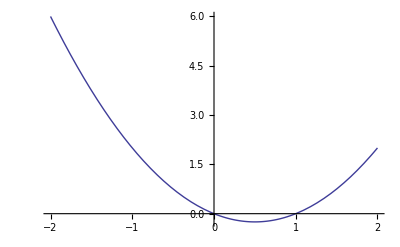

```mathematica
Plot[{t^2-t},{t,-2,2}]
```

As we can see, at x0 =0 and x0 =1, the force on the object is zero and therefore, the particle will not move if we start from these points.

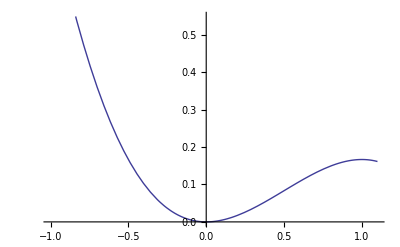

```mathematica
Plot[{-t^3/3+t^2/2},{t,-1,1.1}]
```

Further, as we can see here, the potential energy of the particle has a local maximum at 1.0, a global maximum at -infy and a global minimum at +infy. This is the reason why the value x0= -b/2a is special because the potential energy of the particle at x0= -b/2a= -0.5 is the same as that at x0= 1. for x0 < -0.5, the particle’s energy will diverge, which is what we see in the second case. similarly, as we can see below, for x0 > 1.0, the particle’s trajectory will diverge.

{{x→InterpolatingFunction[{{0.,20.}},<>]}}

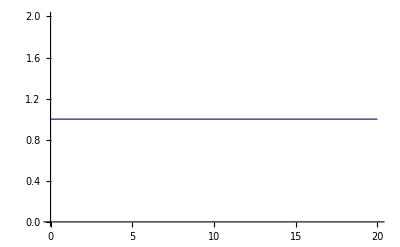

```mathematica
x0 =1;a=1;b=1;m=1;
sol1 = NDSolve[{m*x''[t]==a*x[t]^2-b*x[t],x[0]==x0, x'[0]==0},x,{t,0,20}]
Plot[x[t]/.sol1, {t,0,20}]
```

```mathematica
x0 =2;a=1;b=1;m=1;
sol1 = NDSolve[{m*x''[t]==a*x[t]^2-b*x[t],x[0]==x0, x'[0]==0},x,{t,0,20}]
Plot[x[t]/.sol1, {t,0,20}]
```

NDSolve::ndsz: At t == 2.48405, step size is effectively zero; singularity or stiff system suspected.

{{x→InterpolatingFunction[{{0.,2.48405}},<>]}}

-Graphics-

We also see near-divergent behavior at x0 close to -0.5 and x0 close to 1.0

{{x→InterpolatingFunction[{{0.,100.}},<>]}}

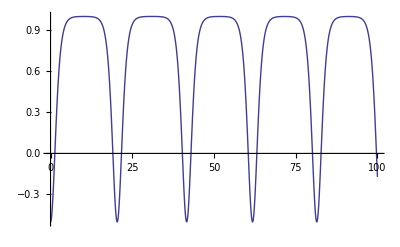

```mathematica
x0 =-0.5;a=1;b=1;m=1;
sol1 = NDSolve[{m*x''[t]==a*x[t]^2-b*x[t],x[0]==x0, x'[0]==0},x,{t,0,100}]
Plot[x[t]/.sol1, {t,0,100}]
```

{{x→InterpolatingFunction[{{0.,100.}},<>]}}

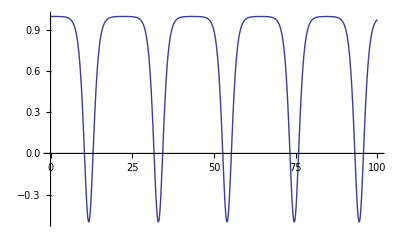

```mathematica
x0 =0.9999;a=1;b=1;m=1;
sol1 = NDSolve[{m*x''[t]==a*x[t]^2-b*x[t],x[0]==x0, x'[0]==0},x,{t,0,100}]
Plot[x[t]/.sol1, {t,0,100}]
```

```mathematica
x0 =1.000000001;a=1;b=1;m=1;
sol1 = NDSolve[{m*x''[t]==a*x[t]^2-b*x[t],x[0]==x0, x'[0]==0},x,{t,0,100}]
Plot[x[t]/.sol1, {t,0,100}]
```

NDSolve::ndsz: At t == 22.4365, step size is effectively zero; singularity or stiff system suspected.

{{x→InterpolatingFunction[{{0.,22.4365}},<>]}}

-Graphics-